# Probability Theory

# Preamble

Probability theory is the mathematics of probability distributions. Given a characterization of a distribution—usually a PF, PDF, or CDF—we may infer certain probabilities. According to probability theory, probabilities are numbers satisfying certain axioms. Any interpretation of those numbers is our own. There are various ways probabilities are inferred or assigned:

symmetry—we ascribe each of 52 cards an equal probability of being drawn;

personal judgement—we look at the sky and contemplate the probability of rain;

data analysis—we repeat an experiment a number of times and analyze the results.

With other words, The term probability refers to the study of randomness and uncertainty. In any situation in which one of a number of possible outcomes may occur, probability theory provides methods for quantifying the chances, or likelihoods, associated with the various outcomes. 

Statistics is a body of techniques for inferring or assigning probabilities based on data. Objective and subjective interpretations of probability support competing statistical traditions.

The objectivist tradition, called Classical statistics : (Frequentist) probability =  long run relative frequency of occurrence.
The subjectivist tradition, called Bayesian statistics : (Bayesian) probability = defined as a degree of belief.

One important consequence of the probability definition is that Bayesian statisticians assign probability distributions to uncertain variables such as parameters, predictions etc, while classical statisticians cannot assign probabilities to all uncertain variables e.g., parameters, instead confidence intervals and regions are used to quantify the parameters uncertainty.

A frequentist would not accept a parameter as a random variable, because randomness, for a frequentist, is associated with variation in replicated observations (and a parameter is neither observed nor can it vary). A Bayesian, in contrast, can see a parameter as a random variable, because for a Bayesian randomness is “lack of knowledge” or “uncertainty in judgement”, that can refer to unseen data just as well as to observable but not replicable events and to unobservable things like parameters.

Parameters describe random vectors much as we might use height or age to describe a person. Formally, a parameter is a function that is applied to a random vector’s probability distribution. It may take on real, vector, or matrix values. A standard deviation, mean vector, or covariance matrix are all examples of parameters. 

Parameters for random variables :

Expectation : E(X) = ∑_x xϕ(x) where for a discrete variable ϕ is the PF ... E(X) = ∫_(-∞)^∞ xϕ(x)ⅆx  here for continuous instead is the PDF

Expectation of a function of a random variable : E[f(X)] = ∑_x f(x)ϕ(x) or E(X) = ∫_(-∞)^∞ f(x)ϕ(x)ⅆx both are generalizations of the above E(X)

Variance :   measures how dispersed a random variable’s probability distribution is, denoted as : var(X) = E[(X-µ)^2]

Skewness : measure the asymmetry of a random variable’s probability distribution, defined as : skew(X) = E[(X-µ)^3]/σ^3

Kurtosis : is a measure of the “tailedness” of the probability distribution, defined as : kurt(X) = E[(X-µ)^4]/σ^4

Quantiles : cut points dividing the range of a probability distribution into continuous intervals with equal probabilities

Moments : for any positive integer k, the k^th moment of a random variable X is defined as : µ’x = E(X^k) and the Central Moment as : µ_k= E[(X-µ)^k]

Based upon our earlier definitions, the expectation and variance of a random variable are its first moment and second central moment. Its skewness and kurtosis are scaled third and fourth central moments.

Random vector X can be thought of as an n-dimensional vector of random variables Xi all defined on the same sample space. It is important to distinguish between a random vector X and a realization of that random vector, which we may denote x. The realization is an element of the range of the random vector. If X and Y simply have the same probability distribution, we denote this relationship X ~ Y. We also use the symbol ~ to indicate what a random variable represents, say: X ~ B(n, p) .. the random vector X is/has a binomial distribution.

Add Parameters of Random Vectors from here : https://www.value-at-risk.net/parameters-of-random-vectors/

The sample space of an experiment, denoted by , is the set of all possible outcomes of that experiment.

An event is any collection of outcomes contained in the sample space. 
An event is simple if it consists of exactly one outcome and compound if it consists of more than one outcome.

# Discrete Random Variables

Probability Mass Function (PMF)

aka Discrete (the number of permitted values is  finite) Density Function
tells us the probability p_j a certain outcome x_j has.

f_x(x_j)=p_j

In order for f_x to be a valid probability density function, p_j must satisfy ..

0≤p_j ≤1
∑_(j=1)^J p_j=1

Probabilities can't be negative and must sum up to 1. That means intuitively that for a certain outcome we're 100% sure that is that outcome and not another ... aka the outcomes are mutually exclusive and collectively exhaustive.

BTW, in the frequentist interpretation of probability: the probability of an event is the relative frequency of its occurrence in a large number of samples.


Note: X is stochastic while x is deterministic. Let’s say X is the number we get from rolling a die. X can take any number between 1-6 .. but once the die is rolled, the value of X is determined as x. The notation X=x means that the variable X takes the particular value of x. X is a random variable while x are random variates. In the language of statistics x is a parameter and X̂ is a statistic that estimates the parameter x.
We assume that our original problem can be put in the following form. There is a probability space (Ω, P) and a random variable X on it. The quantity we want to compute is the mean of X which we denote by µ = E[X]. (The sample space Ω is the set of possible outcomes. Subsets of Ω are called events (x_i), and the probability measure P a function that assigns a number between 0 and 1 to each event.

Note2: when we write f(x) we mean function of x. In mathematics, a function is a binary relation over two sets that associates to every element of the first set exactly one element of the second set. So the above means that for any xj we are associating a probability pj to it or also that p equals f of x (p=f(x)). This build up also the concept of ‘countable’.. so a set A is countable if there exists a function f:Ν⇒A which is bijective (one-to-one and onto). A random variable generally will take only countable many values.

Note3: the set of all pairs of a function (here x,p) is called a graph.. when the domain (X, here also called sample space) and the codomain (P) are sets of real numbers each pair may be considered as the Cartesian coords of the point in the plane... so fx is the point in the plane (sample), the x-axes is xj and the y-axes is pj... the die face 1 (x_1) has  p_1=1/6. In other words.. f(x) is the height of the PMF graph at X=x.

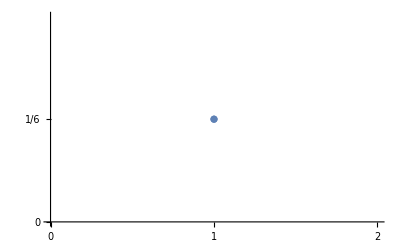

```mathematica
ListPlot[{{1,1/6}},AxesStyle->{Directive[Red,12],Green},Ticks->{{0,1,2},{0,1/6}}]
```

Expectation aka Mean ( µ )

E[X]=∑_(j=1)^J x_j p_j

This means that the summation of all possible outcomes times the probability of the single outcome matches the means of the outcomes, aka the mean is the weighted average of the values taken by X (our random variable), where each weight is specified according to the respective probability.

(The mean is also called the first moment aka the centroid in mechanics. More generally in mathematics a ‘moment’ is quantitative measure of the shape of a function)

It can also be expressed (in frequentist terms) as the sum of values taken by X over a large number of realizations (lim_(t→∞) ) divided by the number of realizations (t) i.e.

(Mean)=lim_(t→∞) 1/t ∑_(j=1)^J x_jt

Where the probability of a given event/outcome is :

lim_(t→∞) (t of x_j)/nt


A population is a collection of items of interest. A sample is a portions of a whole and is representative of the whole.
The population mean is represented by the Greek letter mu (μ). The sample mean is represented by x̄ (Xbar).

Notes:
- if the expectation E[X] exists, we say that X is integrable.
- if E[X^2]<∞ (i.e. if X^2 is integrable), X is called square-integrable
- if E[|X|^m]<∞, for some m>0, we say that X has a finite m-th moment
- if X has a finite m-th moment, the expectation E[|X-E[X]|^m] exists and we call it the m-th central moment

Variance ( σ^2 )

The variance (σ2) is a measure of how far each value in the data set is from the mean. So the variance (also called the second moment about the mean, where skewness is the third moment.) measures the spread of the values about the mean and is defined by :

Var[X]≡E[(X-µ)^2]=∑_(j=1)^J (x_j-µ)^2 p_j

or equivalently

Var(X)=(∑_(j=1)^n p_j x_j^2)-μ^2

Literally, we’re subtracting the mean from each value in the data. This gives us a measure of the distance of each value from the mean. Then squaring each of these distances (so that they are all positive values) and add all of the squares together. Finally divide the sum of the squares by the number of values in the data set.. i.e. it’s the average of the squares of all the deviations.

σ^2=(∑_(j=1)^J (X-µ)^2)/N = 1/N∑_(j=1)^J (X-µ)^2

Take care with relative samples, we use the Bessel’s correction :

σ^2=(∑_(j=1)^J X^2)/(N-1)-N/(N-1)µ^2

That is, when we don’t use the whole population but only a sample of that, instead to divide by 𝓃, we divide by 𝓃-1 to have a better approximation. This can be seen also in this way: when n=4 as soon we got relative bias (x_(j→3)-x^-) for three of them, the fourth can be automatically calculated, so only three where freely determined (ie. 3 degree of freedom.. N-1 degree of freedom).

That is how the samples variance is determined. 
However we may want to calculate the variance of the sampling distribution of the mean.

σ_µ^2=σ^2/N

That is, the variance of the sampling distribution of the mean is the population variance divided by N, the sample size (the number of scores used to compute a mean). Thus, the larger the sample size, the smaller the variance of the sampling distribution of the mean.


The variance of a set of n equally likely values can be equivalently expressed, without directly referring to the mean, in terms of squared deviations of all points from each other: 

Var(X) = 1/n^2∑_(i=1)^n ∑_(j=1)^n 1/2(x_i-x_j)^2

Standard Deviation ( σ )

measures the likely (or expected) deviation in the pay-off from the expectation (i.e. the mean). 
The standard deviation is seen as the width of the distribution.

σ=√Var[X]

The standard error of the mean instead is the standard deviation of the sampling distribution of the mean. It is therefore the square root of the variance of the sampling distribution of the mean and can be written as:

σ_µ^2=σ^2/N

Example : Rolling a die

A random variable X takes on one of the six possible values (x_(j→6)) so its sample space is Ω={1,2,3,4,5,6}.
A fair die has the equal probability of producing one of the six outcomes (X=x_j=j with probability 1/6)
Let us now characterize the probability mass function in terms of the mean and variance.

```mathematica
Clear[xj,t,p,µ,σ2,o2,σ];
xj=1;                                                                          (*occurrences*);
t=6;                                                                             (*total possible realizations*)
p=xj/t;                                                                    (*occurrences of x / total possible realizations*)

µ=Sum[x*p,{x,1,6}]                                         (*mean*)
σ2=Sum[x^2*p,{x,1,6}]-µ^2                            (*variance*)
o2=(Sum[x^2,{x,1,6}]/t)-µ^2//N
σ=√o2                                                                        (*standard deviation*)
```

7/2

35/12

2.91667

1.70783

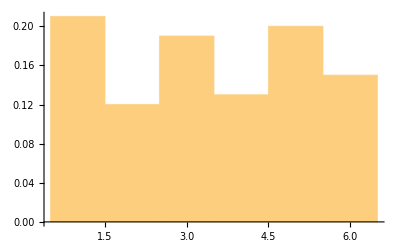

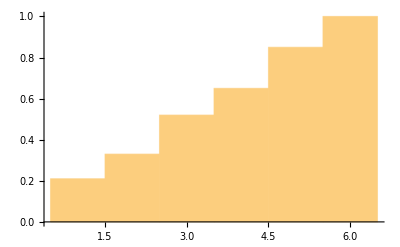

```mathematica
Clear[X,t];
t=100;
SeedRandom[1234];                                                 
X=RandomInteger[{1,6},t];                          (*let a die roll N times*)
Histogram[X,Automatic,"PDF"]                      (*Discrete PDF.. aka PMF*)
Histogram[X, Automatic,"CDF"]                     (*Cumulative Density Function*)
```

Now let’s see if the law of big numbers holds here ...
PMF of rolling a die should be a Uniform Distribution because each outcome should have the equal probability of 1/6.
But we don’t see that from above when rolling a die just 100 times. Let’s try it with 1 million ..

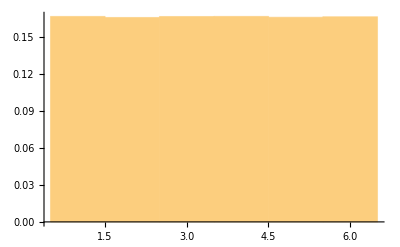

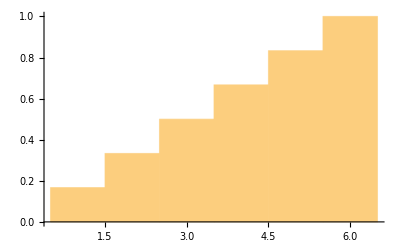

```mathematica
Clear[X,t];
t=1000000;
X=RandomInteger[{1,6},t];
Histogram[X,Automatic,"PDF"]
Histogram[X, Automatic,"CDF"]
```

```mathematica
(*let's check if we have the same sampling variance*)
Clear[X2,var,mvar];
X2=Map[#^2&,X];                                    (*square each element of the list*)
var=(Total[X2]/t)-µ^2//N                  (*sum each squared element, then divide it and substract the squared mean*)

(*what's changed is the mean variance.. as we have more samples it will be lower*)
mvar =var/t
```

2.93205

2.93205×10^-6

Uniform Discrete Distribution

We see that with 1mil tries we are approaching a uniform distribution where each of the faces has the same probability to come out.. i.e. 1/6 or as we see from the PMF graph above around 0.166. (At this point it may make more sense even the CDF.. what is telling us ? That at each outcome we have a 1/6 N accumulated probability). Eventually, change the original seed above to see that this holds for any simulation. Start lowering the number of rolls to see till what limit we get the same uniform distribution.

The uniform (also called rectangular.. look above..) distribution is characterized by each event having an equal probability. It is described by two integer parameters, a and b, which assign the lower and upper bounds of the sample space, respectively. The mean and variance of a (discrete) uniform distribution are given by:

µ=(a+b)/2 ; σ^2=(J^2-1)/12

While the PDF is :

f(x)=1/(B-A) for A≤x≤B

Where A is the ‘location parameter’ and B is the ‘scale parameter’. Not to be confused with the above lowercase a,b which is an interval.

One thing to note. What does mean that here the mean is 7/2 .. i.e. that the most probable outcome is 3.5 ? Dice do not have 3.5 on their faces, right ? Just look at the graph above.. see that the median (the middle of the graph) is 3.5 ... what that means ? That if you bet 6$ each time a 6 is rolled, 5$ for a 5 and so on.. you’ll effectively earn 3.5$ per roll. 

Then another thing to note is: what does mean that the mean and the median are the same ? That the distribution is not skewed and is symmetrical. The more skewed is the distribution, the greater is the difference between the median and mean.

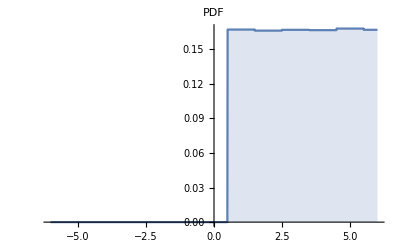
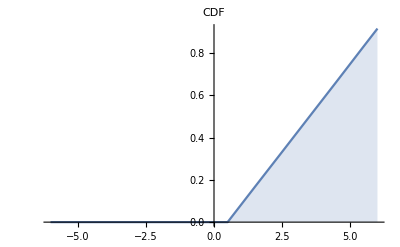

3.502

3.00136

```mathematica
(*using build-ins*)
𝒟=HistogramDistribution[X];
DiscretePlot[#[𝒟,x],{x,-6,6,0.01},PlotLabel->#]&/@{PDF,CDF}
Mean[𝒟]
Variance[𝒟]
```

```mathematica
(*A fair six-sided die can be modeled using a DiscreteUniformDistribution*)
dice=DiscreteUniformDistribution[{1,6}];

(*Generate 10 throws of a die:*)
RandomVariate[dice,10]

(*Compute the probability that the sum of three dice values is less than 6:*)
Probability[Sum[x[i],{i,3}]≤6,{x[1]\[Distributed]dice,x[2]\[Distributed]dice,x[3]\[Distributed]dice}]
```

{1,4,2,2,5,6,1,3,2,1}

5/54

Bernoulli Distribution

The Bernoulli distribution is the discrete probability distribution of a random variable which takes a binary output : 
1 with probability p, and 0 with probability (1-p).

Note: random variables for which S=[0,1] are called indicators. The name comes from the fact that you should think of such variables as signal lights; if X = 1 an event of interest has happened, and if X = 0 it has not happened. In other words, X indicates the occurence of an event.


f(x)={_0^(p^x(1-p)^(1-x))}

Knowing that the expected probability (E) for a discrete distribution is :
 
 E[X]=∑_(j=1)^J x_j p_j
 
 Being x 0 or 1 .. it follows that :
 
 E(x)=0 p^0(1-p)^(1-0) + 1 p^1(1-p)^(1-1)=0+p=p
 
 
 Same goes for the Variance.. knowing that :
 
 Var[X]≡E[(X-µ)^2]f(x)= E(X^2)-E^2(X)

Where :

E(X^2)= ∑_(x=0)^1 x^2 p(x) =∑_(x=0)^1 x^2 p^x(1-p)^(1-x) =0^2 p^0(1-p)^(1-0) + 1^2 p^1(1-p)^(1-1)=p

and (from above expected probability)

E^2(X)=p^2

then 

V(X)=p-p^2=p(1-p)



Examples

1) A basketball player has a free-throw percentage of 0.75. Simulate 10 free shots.

```mathematica
RandomVariate[BernoulliDistribution[0.75],10]/.{0->"Miss",1->"Hit"}

(*Find the probability that the player hits 2 out of 3 free shots in a game:*)
Probability[x==2,x\[Distributed]BinomialDistribution[3,0.75]]
```

{Miss,Hit,Miss,Hit,Hit,Hit,Hit,Hit,Miss,Miss}

0.421875

2) A family with two children is known to have a boy. Assuming boys and girls are equally likely among newborns, find the probability that the other child is a girl:

```mathematica
Probability[(fc==1||sc==1)\[Conditioned](fc==0||sc==0),{fc,sc}\[Distributed]ProductDistribution[BernoulliDistribution[1/2],BernoulliDistribution[1/2]]]
```

2/3

Here we see a product distribution of two Bernoulli random variables.

A product distribution is a probability distribution constructed as the distribution of the product of random variables having two other known distributions. Given two statistically independent random variables X and Y, the distribution of the random variable Z that is formed as the product

Z=XY

is a product distribution.

Binomial Distribution

the idea behind the Bernoulli distribution is that the experiment is repeated only once. 
But what happens if we run more than one trial, under the assumption that trials are independent among each other ?
The answer is the Binomial Distribution. 
This distribution describes the behavior the outputs of n random experiments, each having a Bernoulli distribution with probability p.

For example, let’s say we flip 5 times a coin (or flip 5 coins..), getting the following results : 

0 0 0 1 1

Then we had :

(1-p) (1-p) (1-p) (p) (p) 

And since trials are independent, we can write it like : 

(1-p)^3 p^2

Hence, the probability of getting exactly k successes in n independent Bernoulli trials is given by the probability mass function:

f(k,n,p)=(_k^n)p^k(1-p)^(n-k)

Now, let’s say we flip 3 times a coin and we win if we have at least one head.. this can be modelled with the Binomial Coefficient :

c(n,k)=(_k^n)=(n!)/(k!(n-k)!)

note: this also model Permutations where order does not matter.. i.e. Combinations.. where repetitions are not allowed (events are indipendent from each others) ..
i.e. in order to arrive at the number of Combinations, one needs to figure out all the Permutations (n!) and divide by all Redundancies (where a group has the same events just in a different order). BTW, if instead we have really Permutations with indipendent events than we just remove k! from the denominator.. n!/(n-k)!


So we get :

f[k_,n_,p_]:=(n!)/(k!(n-k)!)p^k(1-p)^(n-k)

This let us answer to questions like this.. suppose that 80% of adults with allergies report symptomatic relief with a specific medication. If the medication is given to 10 new patients with allergies, what is the probability that it is effective in exactly seven?

# observation is n=10
# successes or events of interest is k=7
# p=0.80


It’s important to note that if n tends towards infinite and both p and (1-p) are not indefinitely small, it well approximates a Gaussian distribution. The latter is hence a limiting form of Binomial distribution. 

Let’s just test that the distribution has a Gaussian (kinda bell) shape.

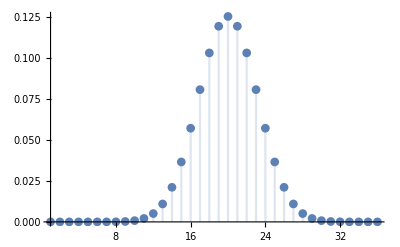

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[40,p],k],{p,{0.5}}]//Evaluate,{k,36},PlotRange->All,PlotMarkers->Automatic]
```

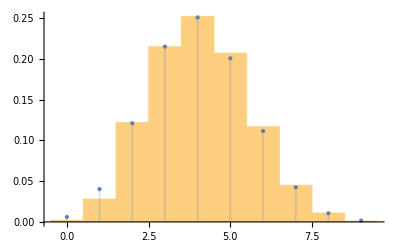

```mathematica
Clear[data];
SeedRandom[123];
data=RandomVariate[BinomialDistribution[10,0.4],10^3]; (*gen 1000 trials where each is composed of 10 events with a 40% p*)
Show[Histogram[data,{1},"PDF"],DiscretePlot[PDF[BinomialDistribution[10,0.4],x],{x,0,10},PlotStyle->PointSize[Medium]]]
```

```mathematica
Clear[f,n,k,p];
f[k_,n_,p_]:=(n!)/(k!(n-k)!)p^k(1-p)^(n-k);

CDF[BinomialDistribution[x,p],k]
```

Piecewise[{{BetaRegularized[1-p,x-Floor[k],1+Floor[k]], 0≤k<x}, {1, k≥x}, {0, True}}]

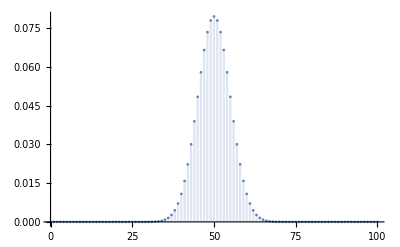

0.028444

```mathematica
(*The number of heads in n flips with a fair coin can be modeled with a BinomialDistribution*)
heads[n_]:=BinomialDistribution[n,1/2];

(*Show the distribution of heads for 100 coin flips:*)
DiscretePlot[PDF[heads[100],k],{k,0,100},PlotRange->All]

(*Compute the probability that there are between 60 and 80 heads in 100 coin flips:*)
Probability[60≤x≤80,x\[Distributed]heads[100]]//N
```

Geometric Distribution

Binomial distribution describes the number of successes k achieved in n trials, where probability of success is p. Negative binomial distribution describes the number of successes k until observing r failures (so any number of trials greater then r is possible), where probability of success is p. Geometric distribution is a special case of negative binomial distribution, where the experiment is stopped at first failure (r=1). So while it is not exactly related to binomial distribution, it is related to negative binomial distribution.

The following is an example for the difference between the Binomial and Geometric distributions: If a family decides to have 5 children, then the number of girls (successes) in the family has a binomial distribution. If the family decides to have children until they have the first girl and then stop, then the number of children in the family has a Geometric distribution (the number can be 1,2,... and is in theory unbounded).

Generally, binomial variable considers the successes and the geometric variable considers the number of trials.

The geometric distribution represents the number of failures before you get a success in a series of Bernoulli trials. 
This discrete probability distribution is represented by the PDF(PMF):
f_X(x) = (1-p)^(x-1)p

CDF:
F_(X(x)) = 1-(1-p)^x

Mean:
1/p

Variance :
(1-p)/p^2


Now let’s say you ask people outside a polling station who they voted for until you find someone that voted for the independent candidate in a local election. The geometric distribution would represent the number of people who you had to poll before you found someone who voted independent. You would need to get a certain number of failures before you got your first success.

If you had to ask 3 people, then X=3; if you had to ask 4 people, then X=4 and so on. In other words, there would be X-1 failures before you get your success.

If X=n, it means you succeeded on the nth try and failed for n-1 tries. The probability of failing on your first try is 1-p. For example, if p = 0.2 then your probability of success is .2 and your probability of failure is 1 – 0.2 = 0.8.

Because the trials are indipendent (i.e. Bernoulli trials) it means that you can multiply the probabilities together.
So the probability of failing on your second try is (1-p)(1-p) and your probability of failing on the nth-1 tries is (1-p)^(n-1). If you succeeded on your 4th try, n = 4, n – 1 = 3, so the probability of failing up to that point is (1-p)(1-p)(1-p) = (1-p)^3.


Examples

1) If your probability of success is 0.2, what is the probability you meet an independent voter on your third try?
Inserting 0.2 as p and with X=3 in the above fnc, the probability density function becomes:

P(X=3) = (0.8)^(3-1)*0.2 = 0.128


2) A person is standing by a road counting cars until he sees a black one, at which point he restarts the count. Simulate the counting process, assuming that 10% of the cars are black:

{17,3,4,9,13,16,4,10,2,9,10,11,1,13,19,16,6,11,4,14}

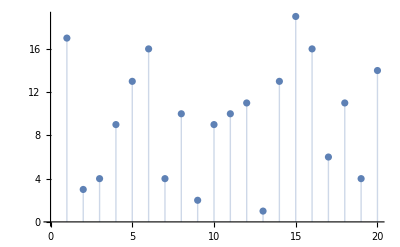

```mathematica
RandomVariate[GeometricDistribution[10/100],20]
ListPlot[%,Filling->Axis]
```

```mathematica
(*Find the expected number of cars to come by before the count starts over:*)
Mean[GeometricDistribution[0.1]]

(*Find the probability of counting 10 or more cars before a black one:*)
Probability[x≥10,x\[Distributed]GeometricDistribution[0.1]]
```

9.

0.348678

3) A student will take a test repeatedly until passing it, each time succeeding with probability p. 
Find the probability that the student succeeds in k attempts or fewer:

1-(1-p)^(1+k)

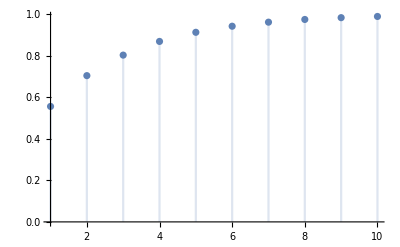

```mathematica
Clear[p1,x,k,p];
p1=Probability[x≤k,x\[Distributed]GeometricDistribution[p],Assumptions->k∈Integers&&k≥0]
Block[{p=1/3},DiscretePlot[p1,{k,10},AxesOrigin->{1,0}]]
```

Piecewise[{{((1-p)^k p)/(1-(1-p)^n+(1-p)^n p), k≤n&&k≥0}, {0, True}}]

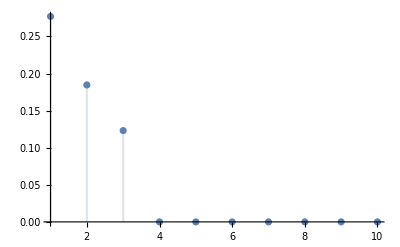

```mathematica
(*Given that the student passes the test in n attempts or fewer,find the PDF:*)
Clear[p2,x,k,p];
p2=Probability[x==k\[Conditioned]x≤n,x\[Distributed]GeometricDistribution[p],Assumptions->{k,n}∈Integers&&n>0]
Block[{p=1/3,n=3},DiscretePlot[p2,{k,10},AxesOrigin->{1,0}]]
```

4) Compute and illustrate the discrete probability P(4≤x≤8)

268679511/1000000000

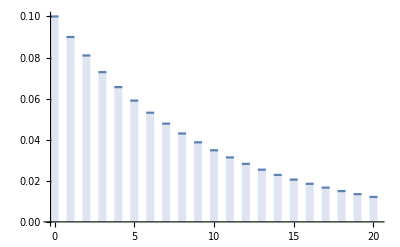
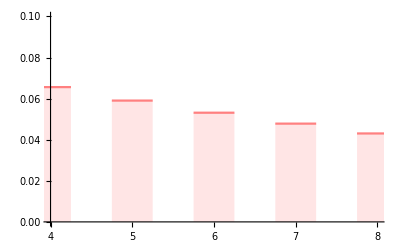

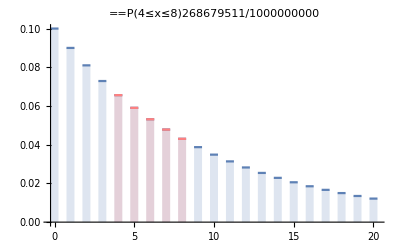

```mathematica
Clear[prob,p1,p2];
prob=Probability[4≤x≤8,x\[Distributed]GeometricDistribution[1/10]]

{p1,p2}={DiscretePlot[PDF[GeometricDistribution[1/10],k],{k,0,20},ExtentSize->0.5],
DiscretePlot[PDF[GeometricDistribution[1/10],k],{k,4,8},ExtentSize->0.5,PlotStyle->Pink,PlotRange->{0,0.10}]}

Show[p1,p2,PlotLabel->Row[{P[4≤x≤8],prob},"="]]
```

# Discrete Bivariate Random Variables (Random Vectors)

Joint Distributions

let us consider rolling two dice. The first die takes on x_i = i, i = 1, . . . , 6, and the second die takes on y_j = j, j = 1, . . . , 6. 
The random vector associated with rolling the two dice is : (X,Y) where X and Y take on J_X and J_Y values, respectively. 
Thus, the random vector (X, Y ) takes on J = J_X · J_Y = 36 values .. aka joint probability distribution.

The probability mass function associated with (X, Y ) is denoted by :

f_(X,Y)(x_i,y_i)=1/6.1/6=1/36

note: the comma means ‘and’ so we can re-write it as : 

f_(X,Y)(x_i,y_i)=f((X=x)and(Y=y)



Marginal probability mass function

If we ignore the outcome of Y , and ask ourselves the question: How frequently does X take on the value x_i? I.e. it gives the probabilities of various values of the variables in the subset without reference to the values of the other variables.

Given a known joint distribution of two discrete random variables, say, X and Y, the marginal distribution of either variable--X for example--is the probability distribution of X when the values of Y are not taken into consideration. This can be calculated by summing the joint probability distribution over all values of Y. Naturally, the converse is also true: we can obtain the marginal distribution for Y by summing over the separate values of X.

p_x(x_i)=∑_j p(x_i,y_j)

or as a marginal density : 

f_x(x_i)=∑_(j=1)^J_Y f_(x,y)(x_i,y_j), i=1,..,J_X

Intuitively, the marginal probability of X is computed by examining the conditional probability of X given a particular value of Y, and then averaging this conditional probability over the distribution of all values of Y.

They are called ‘marginal’ because they’d fill the margins of a table containing the joint distribution values..

```mathematica
Clear[a];
a={{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/36,1/36,1/36,1/36,1/36,1/36,1/6},{1/6,1/6,1/6,1/6,1/6,1/6,1}};
Grid[a,Frame->All,ItemStyle->{Automatic,Automatic,{{{7,7},{1,6}}->Green,{{1,6},{7,7}}->Pink}} ]
```

1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1

In a table (X,Y).. summing all respective columns values (x_i) gives the p_x , while summing all respective row values (y_j) gives the p_y .. and they would be written at the respective (bottom|right) table 'margins'. Of course the bottom/right cell will be 1 .. that also means that marginal densities are valid probability distributions .. i.e.

0≤P_(X,Y) ≤1
∑_(j=1)^J P_(X,Y)=1


Marginal distribution functions play an important role in the characterization of independence between random variables: two random variables are independent if and only if their joint distribution function is equal to the product of their marginal distribution functions.

Let X and Y be two random variables with marginal distribution fncs :

(note: use pw to enter { and ‘CTRL comma’ and then ‘CTRL return’ for each additional piecewise case)

F_X(x)= Piecewise[{{0, if x<0}, {1-exp(-x), if x≥0}}]

F_Y(y)= Piecewise[{{0, if x<0}, {1-exp(-y), if x≥0}}]

and joint distribution function :

F_(X,Y)(x,y)=Piecewise[{{0, if x<0 or y<0}, {1-exp(-x)-exp(-y)+exp(-x-y), if x≥0 and y≥0}}]

So when x<0 or y<0, then

F_x(x)F_y(y)=0=F_(x,y)(x.y)

When x>=0 and y>=0, then :

F_x(x)F_y(y)=[1-exp(-x)][1-exp(-y)]
=1-exp(-x)-exp(-y)+exp(-x)exp(-y)
=1-exp(-x)-exp(-y)+exp(-x-y)
=F_(X,Y)(x,y)

The fact that the probability density is simply a product of marginal densities means that we can draw X and Y separately according to their respective marginal probability and then form the random vector (X, Y ).

p.s.: the inverse process.. i.e. deriving the distribution of a component X of a random vector X,Y from the joint distribution of X,Y is called marginalization. We can also use marginalization to find the joint distribution of X and Y from an X,Y,Z vector (i.e. we marginalized out Z).

 
 
Conditional probability

the probability that X takes on the value x_i given Y has taken on the value y_j . The conditional probability is denoted by :

f_(X|Y)(x_i|y_j), i=1,...,J_X
note: while the marginal uses , ‘and’ conditional uses | ‘or’

and can be expressed as :

f_(X|Y)(x_i|y_j)=(f_(X,Y)(x_i,y_j))/(f_Y(y_j))

In other words, the probability that X takes on x_i given that Y has taken on y_j is equal to the probability that both events take on (x_i, y_j) normalized by the probability that Y takes on y_j disregarding x_i. This is called the conditional distribution of X, given Y = y.


f_X(x_i)=∑_(j=1)^J_Y f(x_i,y_j)=∑_(j=1)^J_Y f_(X|Y)(x_i|y_j)f_Y(y_j)

That means, the marginal probability of X taking on x_i is equal to the sum of the probabilities of X taking on x_i given Y has taken on y_j multiplied by the probability of Y taking on y j disregarding x_i .

1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/36 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1

For example the above is the conditional probability for y=3.



Examples

1) Let’s associate two coin flips with a random vector (X,Y). 

PMF_(x,y)= f_X(x)=1/2; f_Y(y)=1/2

f_(x,y)(x,y)=1/2.1/2=1/4 (joint probability density)

Now, what’s the conditional probability of X taking on 1 given that Y takes on 0 ? (Of course, intuitively.. being independent events.. conditional probability here is the same as probability of the single event)

f_(X|Y)(x=1|y=0)=(f_(x,y)(x=1,y=0))/(f_Y(y=0))=(1/4)/(1/2)=1/2


2) Two fair dice are rolled. What is the probability that at least one lands on 6 given that the dice land on different numbers ?

The probability that one die is six and the other is not is 1/6 5/6 and so is the probability that one die is not 6 and the other is.. 5/6 1/6.
So the joint probability of both dice is 2 1/6 5/6=10/36
And the conditional probability is :f_(X|Y)(x_i|y_j)=(f_(X,Y)(x_i,y_j))/(f_Y(y_j))=(10/36)/(30/36)=1/3



3) If 2 fair dice are rolled, what is the probability that the sum is 6, given both dice show odd numbers ?

Let B be the event “both dice are odd,” and let S6 be the event “the sum is 6.” We want :

Pr(S6|B)

Now we use the formula
Pr(S6|B)Pr(B)=Pr(S6∩B)

Calculating Pr(B) is easy: the answer is 9/36

We know that we have 36 ordered pair but how many have sum 6 and both are odd ? (1,5), (3,3), (5,1). 
We conclude that Pr(S6∩B)=3/36
So the conditional probability is (3/36)/(9/36)=1/3


4) A die is rolled until a 3 or 6 appears, otherwise it is rolled four times. Given that a 3 or 6 did not appear in either of the first two rolls, find the probability for that the die was tossed four times.

Let A denote the event in which 4 rolls where made.
Let B denote the event in which neither 3 nor 6 appeared during the first 2 rolls.

Then P(A|B)=(P(A∩B))/(P(B))=((1 - 2/6)3)/(1-2/6)^2=1-2/6=2/3


5) What is the probability that the total of two dice will be greater than 8 given that the first die is a 6 ?

There are 6 outcomes for which the first die is a 6, and of these, there are four that total more than 8 (6,3; 6,4; 6,5; 6,6). The probability of a total greater than 8 given that the first die is 6 is therefore 4/6 = 2/3.

More formally, this probability can be written as:

p(total>8 | Die 1 = 6) = 2/3

In this equation, the expression to the left of the vertical bar represents the event and the expression to the right of the vertical bar represents the condition. Thus it would be read as “The probability that the total is greater than 8 given that Die 1 is 6 is 2/3.”


6) Let us now consider flipping a single coin. We associate a Bernoulli random variables X and Y with :

x=Piecewise[{{1, head}, {0, tail}}]   and   y=Piecewise[{{1, tail}, {0, head}}]

i.e. when head X is 1 and Y is 0, when tail Y is 1 and X is 0.
First, let us show that these two variables are not independent.

Joint probability density function :

f_(X,Y)(x,y)=Piecewise[{{1/2, (x,y)=(0,1)}, {1/2, (x,y)=(1,0)}, {0, (x,y)=(0,0)or(x,y)=(1,1)}}]

Marginal density of each event is still :

f_X(x)=1/2, x∈{0,1}
f_Y(y)=1/2, y∈{0,1}

For (x,y)=(0,0) we have :

f_(X,Y)(x,y)=0≠1/4=f_X(x)f_Y(y)

that means X and Y are not indipendent (i.e. joint distribution fnc is different from the product of the two marginal density fncs).

We can also consider conditional probabilities. The conditional probability of x = 1 given that y = 0 is :

f_(X,Y)(x=1|y=0)=(f_(X,Y)(x=1,y=0))/(f_Y(y=0))=(1/2)/(1/2)=1

Because of course if Y is 0 then X is for sure 1. 

Now let’s see what are our chances to get X=1 when Y=1 ...

f_(X,Y)(x=1|y=1)=(f_(X,Y)(x=1,y=1))/(f_Y(y=0))=0/(1/2)=0

We have seen that independence is one way of describing the relationship between two events.
Another concept that describes how closely two events are related is correlation, which is a normalized covariance.


7) Let us first revisit the case of flipping two fair coins. The random vector considered in this case is :

(X_1,X_2)

where X 1 and X 2 are independent Bernoulli random variables associated with the first and second flip, respectively. As in the previous coin flip cases, we associate 1 with heads and 0 with tails. There are four possible outcome of these flips :

(0, 0), (0, 1), (1, 0), and (1, 1)

note: because the random variables are independent and each variable has the same distribution, 
they are said to be independent and identically distributed or i.i.d. for short.

From the two flips, we can construct the binomial distribution Z_2 ∼ B(2, θ = 1/2)
The binomial random variable is defined as :

Z_2 = X_1 + X_2

Counting the number of heads associated with all possible outcomes of the coin flip, the binomial random variable takes on the following value:

Z_2 = (0,0=0), (0,1=1), (1,0=1), (1,1=2)

Because the coin flips are independent and each coin flip has the probability density of f_x_1(x)=1/2, x=0,1.. their joint distributions is :

f_(X_1,X_2)(x_1,x_2)=f_X_1(x_1).f_X_2(x_2)=1/2.1/2=1/4

Thus the behavior of the binomial random variable Z 2 can be stated as :

Z_2=Piecewise[{{0,, with prob 1/4}, {1,, with prob 1/4+1/4=1/2}, {2,, with prob 1/4}}]

note: we assign probabilities by invoking the mutually exclusive property, OR (union), and summation.

Eventually, The probability mass function of Z_2 is given by :

f_Z_2=Piecewise[{{1/4,, x=0}, {1/2,, x=1}, {1/4,, x=2}}]




Covariance

The covariance of two random variables X and Y is denoted by Cov(X, Y ) and it is defined as :

Cov(X, Y ) ≡ E[(X − μ X )(Y − μ Y )] 

covariance is the expected value of the product X̄ Ȳ, where X̄ and Ȳ are defined as follows :

X̄= X - E[X]
Ȳ=Y-E[Y]

 X̄ and Ȳ are the deviations of X and Y from their respective means.
 Being a product when X̄ Ȳ is positive it means that either X and Y are both above or both below their respective means.
 On the contrary when X̄ Ȳ is negative, it means that either X is above and Y is below or just the opposite.
 
In other words when X̄ Ȳ is positive, X and Y are concordant (their deviations from the mean have the same sign); 
when X̄ Ȳis negative, X and Y are discordant (their deviations from the mean have opposite signs).

The covariance tells us how similar the deviations of the two variables (from their respective means) are on average.

The covariance between two random variables can also be defined by the formula (equivalent to the above one) :

Cov[X,Y]=E[XY]-E[X]E[Y]


Correlation

Correlation is a measure of dependence between two random variables that can take values between -1 and 1.  It is proportional to covariance and its interpretation is very similar to that of covariance that can be seen as a normalized covariance.

The correlation of X and Y is denoted by ρ_XY and is defined as :

ρ_XY=(Cov(X,Y))/(σ_X σ_Y)

The correlation indicates how strongly two random events are related and takes on a value between −1 and 1. In particular, two perfectly correlated events take on 1 (or −1), and two totally independent events take on 0.

The following terminology is often used:

If ρ_XY>0 then X and Y are said to be positively linearly correlated (or simply positively correlated).

If ρ_XY<0 then X and Y are said to be negatively linearly correlated (or simply negatively correlated).

If ρ_XY≠0 then X and Y are said to be linearly correlated (or simply correlated).

If ρ_XY00 then X and Y are said to be uncorrelated. 


Note that Cov[X,Y]=0=>Corr[X,Y]=0, therefore two random variables X and Y are uncorrelated whenever Cov[X,Y].
Also note that a correlation of a random variable with itself is Corr[X,X]=1.
Eventully note that the linear correlation coefficent (or Pearson’s correlation coefficient) is symmetric : Corr[X,Y]=Corr[Y,X].

# Continuous Random Variables

A continuous random variable is a random variable where the data can take infinitely many values. For example, a random variable measuring the time taken for something to be done is continuous since there are an infinite number of possible times that can be taken.

Probability Density Function

Let X be a random variable that takes on any real value in an interval :

X∈[a,b]

The probability density function (PDF) is a function over [a,b], f_X(x) such that :

f_X(x)≥0, ∀x ∈ [a,b]   (.. in words, f_x is greater or equals to zero and (,) all the possible outcomes (∀) of x belongs to the interval a,b)

∫_a^b f_X ⅆx = 1

that is, the probability that X take on a value over an infinitesimal interval of length dx is :

P(x ≤ X ≤ x+dx) = f_X(x)ⅆx,

or, over a finite subinterval [a',b'] ⊂ [a,b]  (i.e. a',b' is a subset of a,b)

P(a'≤X≤b') = ∫_a'^b' f_X(x)ⅆx

That means, the probability that X takes on the value between a' and b'
is the integral of the probability density function f_X over [a,b].

In other words, for discrete random variables, we look up the value of a PMF at a single point to find its probability P(X=x). For continuous random variables, we take an integral of a PDF over a certain interval to find the probability that X will fall in that interval.

While a PMF describe an exact probability, a PDF describes a density (i.e. an infinitesimal area) where a random value belong to.

So what is the probability that X=x (i.e. =5.00000000000000000000) at a single point ? It is 0. 
We may say that intuitively at a single point the area is zero. Or that having a continuous random variale an infinite set of possible values (even if the domain is set and fixed) while the sum of probabilities is 1, the probability at a single point should be 1/∞ , which is 0.
(This is also why we integrate instead to sum PDFs for continuos random vars).

Cumulative Distribution Function

A particular instance of the above, - is a cumulative distribution function (CDF), F_X(x), 
which describes the probability that X will take on a value less than x, i.e.

F_X(x)=P(X⩽x)

F_X(x) = ∫_a^x f_X(x)ⅆx

In the case of a scalar continuous distribution, it gives the area under the probability density function from minus infinity to x.

Note that any CDF satisfies the conditions :

F_X(a) = ∫_a^a f_X(x)ⅆx=0,   F_X(b) = ∫_a^b f_X(x)ⅆx=1

furthermore, it easily follows that :

P(a'⩽X⩽b') = F_X(b') - F_X(a')

That is, 
we can compute the probability of X taking on a value in [a', b'] by taking the difference of the CDF evaluated at the two end points.


Every cumulative distribution function  F_X is monotonically (i.e. iif is entirely) non-decreasing and right-continuous, which makes it a càdlàg function. Furthermore :

lim_(x→-∞) F_X(x)=0,    lim_(x→+∞)F_X(x)=1

Every function with these four properties is a CDF, i.e., for every such function, a random variable can be defined such that the function is the cumulative distribution function of that random variable.


The probability density function of a continuous random variable can be determined from the cumulative distribution function by differentiating using the Fundamental Theorem of Calculus; i.e. given F_X,

f(x) = (ⅆF(x))/ⅆx    (as long as the derivative exists)

Mean, Variance and Quantiles

The mean, µ, or the expected value, E[X], of the random variable X is : 

µ = E[X] = ∫_a^b f(x)ⅆx = ∫_a^b ⅆF(x)-μ^2


Where f(x) is the variance, Var(X), i.e. the measure of the spread of the values that X takes about its mean and is defined by : 

Var(X) = E[(X-µ)^2] = ∫_a^b (x-µ)^2 ⅆx = ∫_a^b x^2 f(x)ⅆx-μ^2
Var(X) = E[X^2]-µ^2


The α-th quantile(or percentile) of a random variable X is denoted by (z̃)_α (tilde is AltGr+ì in Linux) and satisfies :

F_X((z̃)_α) = α

In other words, the quantile (z̃)_α partitions the interval [a,b] such that the probability of X taking on a value in [α,(z̃)_α] is α 
(and conversely P((z̃)_α⩽X⩽b)=1-α. The α=1/2 quantile is the median.

The cumulative distribution function (shown as F(x)) gives the p values as a function of the q values. The quantile function does the opposite: it gives the q values as a function of the p values. That’s why it is also called inverse cumulative distribution function.

The three “named” percentiles are Q1 — the first quartile, or the 25th percentile; Q2 — the 2nd quartile (also known as the median or the 50th percentile); and Q3 — the 3rd quartile or the 75th percentile.

Quantiles, also called Percentiles, are also used in boxplots for displaying the distribution of data based on a five number summary (min, 1stQ, median, 3rdQ and max).

Uniform Distribution

Let X be a uniform random variable. Then, X is characterized by a constant PDF,

f_X(x) = f^uniform(x;a,b) ≡ 1/(b-a)


Note that the PDF satisfies the constraint 

∫_a^b f_X(x)ⅆx = ∫_a^b f^uniform(x;a,b)ⅆx = ∫_a^b 1/(b-a)ⅆx=1


Furthermore, the probability that the random variable takes on a value in the subinterval [a',b']∈[a,b] is

P(a'≤X≤b') = ∫_a'^b' f_X(x)ⅆx = ∫_a'^b' f^uniform(x;a,b)ⅆx = ∫_a'^b' 1/(b-a)ⅆx = (b'-a')/(b-a)

In other words, the probability that X ∈ [a', b'] is proportional to the relative length of the interval as the density is equally distributed.

The distribution is compactly denoted as 𝒰(a,b) and we write X~𝒰(a,b).


A straightforward integration of the PDF shows that the CDF of X~𝒰(a,b) is 

F_X(x) = F^uniform(x;a,b) ≡ (x-a)/(b-a)


The mean of the uniform distribution is given by

E[X] = ∫_a^b f_X(x)ⅆx = ∫_a^b x 1/(b-a)ⅆx = 1/2(a+b)

This agrees with our intuition, because if X is to take on a value between a and b with equal probability, then the mean would be the midpoint of the interval.


Finally the variance of the uniform distribution of continuous random variables is 

Var(X) = E[(X^2)]-(E[X])^2 = ∫_a^b x^2 f_X(x)ⅆx-(1/2(a+b))^2 = ∫_a^b x^2/(b-a)ⅆx-(1/2(a+b))^2 = 1/12(b-a)^2

```mathematica
(* Use Mathematica to exploit uniform distributions *)
Clear[a,b,x];
PDF[UniformDistribution[{a,b}],x]
CDF[UniformDistribution[{a,b}],x]

Mean[UniformDistribution[{a,b}]]
Variance[UniformDistribution[{a,b}]]
Covariance[UniformDistribution[{{a,b},{c,d}}]]//MatrixForm
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

Piecewise[{{(-a+x)/(-a+b), a≤x≤b}, {1, x>b}, {0, True}}]

(a+b)/2

1/12 (-a+b)^2

(1/12 (-a+b)^2 | 0
0 | 1/12 (-c+d)^2)

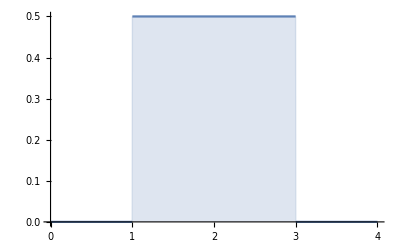

```mathematica
(* Probability density function of univariate uniform distribution *)
Plot[PDF[UniformDistribution[{1,3}],x]//Evaluate,{x,0,4},PlotRange->All,Filling->Axis]
```

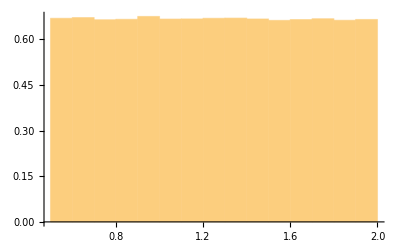

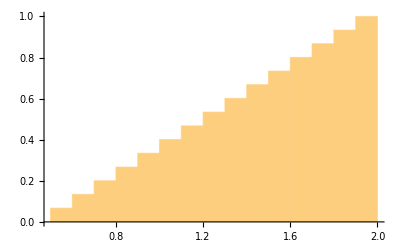

```mathematica
(* Shot 1M uniform randoms between 0.5,2 .. aka shot 1M random number with a uniform distribution *)
Clear[data];
data=RandomVariate[UniformDistribution[{0.5,2}],10^6];
Show[Histogram[data,20,"PDF"]]
Show[Histogram[data,20,"CDF"]]
```

Example


1) Old Faithful erupts every 91 minutes. You arrive there at random and wait for 20 minutes ... what is the probability you will see it erupt ?
This is actually easy to calculate, 20 minutes out of 91 minutes is:

p = 20/91 = 0.22 (to 2 decimals)

But let’s use the Uniform Distribution for practice.

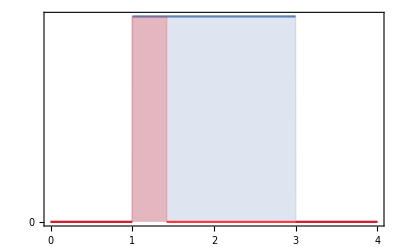

```mathematica
Clear[p1,p2];
p1=Plot[PDF[UniformDistribution[{1,3}],x]//Evaluate,{x,0,4},PlotRange->All,Filling->Axis,Frame->True,FrameTicks->{
{{0,1,1.42,2,3,4},None},{{{0,0},{1,1},{1.42,""},{2,2},{3,3},{4,4}},{{0,""},{1,"a"},{1.42,"a+20"},{2,""},{3,"a+91"}}}
},FrameTicksStyle->Directive[Orange,12]];
p2=Plot[PDF[UniformDistribution[{1,1.42}],x]//Evaluate,{x,0,4},PlotRange->{{0,1.42},{0,0.5}},Filling->Axis,PlotStyle->{Red, Opacity[0.75]}];
Show[p1,p2]
```

Now, to find the probability between a and a+20, just find the red area.. we know that the heigh is 1/b-a.. so in this case is 1/91 (i.e. 1/a+91-a).. while the on the x axes we need to do a+20-a, that reduce to 1/91*20, which is 20/91=0.22


2) Two trains arrive at a station independently and stay for 10 minutes. If the arrival times are uniformly distributed, find the probability the two trains will meet at the station within one hour:

```mathematica
Probability[Abs[x-y]<10,{x,y}\[Distributed]UniformDistribution[{{0,60},{0,60}}]]
```

11/36

3) Generate uniformly distributed random numbers in the 0,1 interval

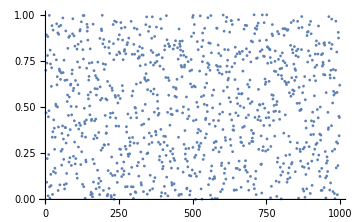

```mathematica
Clear[𝒟,data];
𝒟=UniformDistribution[{0,1}];
data=RandomVariate[𝒟,1000];
ListPlot[data,ImageSize->Medium]
```

We can also use the so called ‘inversion method’. 
We just use a random number and plug it into the inverse of the CDF of a certain distribution.

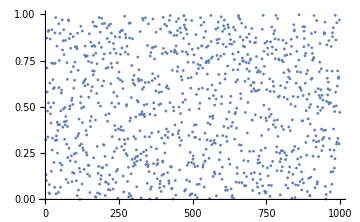

```mathematica
data=Table[InverseCDF[𝒟,RandomReal[]],1000];
ListPlot[data,ImageSize->Medium](*test visually they are uniformly distributed*)
(* of course RandomReal[] is already ~U(0,1) , see part3 for more meanful applications*)
```

Normal Distribution

Let X be a normal random variable. Then the PDF of X is of the form :

f_X(x) = f^normal(x;μ,σ^2) ≡ 1/(√(2 π) σ)ⅇ^(-(x-µ)^2/(2 σ^2))

The PDF is parametrized by two variables, the mean μ and the variance σ^2.. X_(μ,σ^2) .. thus is denoted by X ∼ 𝒩(μ,σ^2).

The CDF of a normal distribution takes the form :

F_X(x)=1/2 erf[(-x+µ)/(√2 σ)]

where erf is the error function, given by 

erf(x)=2/π∫_0^x e^(-z^2)ⅆz


The simplest case of a normal distribution is known as the standard normal distribution. 
This is a special case when μ=0 and σ=1, and it is described by this PDF:

f_X(x)=φ(x)=1/(√(2π))e^(-x^2/2)

The factor 1/√(2π) ensures that the total area under the curve φ(x) is equal to one. The factor 1/2 in the exponent ensures that the distribution has unit variance, and therefore also unit standard deviation. This function is symmetric around x=0, where it attains its maximum value 1√(2π) and has inflection points at x=+1 and x=-1.

```mathematica
Clear[p1,p2,p3,p4,x];
p1=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-4,4},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,0.1,0.2,0.3,0.4,0.5}},AxesLabel->{X,Subscript[φ, μ,σ^2(X)]},AxesOrigin->{-4,0}];
p2=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-1,1},Filling->0,PlotStyle->{Red, Opacity[0.75]}];
p3=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-2,2},Filling->0,ColorFunction->Function[{horiz,vert},Opacity[.2,ColorData["Aquamarine"][horiz]]]];
p4=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-3,3},Filling->0,PlotStyle->{White, Opacity[0.25]}];
Show[p1,p2,p3,p4]
```

-Graphics-

When a normal distribution is normalized it becomes a standard normal distribution. 
The ticks on the x-axes are the standard deviations from the mean (that for a standard normal distribution correspond to) : 

- the pinkish area is within 1SD of the mean and it covers the 68% of the distribution
- the aquamarine is within 2SD and covers up 95%
- the grey is within 99.7% and is within 3SD

(this is the empirical rule, also referred to as the three-sigma rule or 68-95-99.7 rule)

A PDF is used to specify the probability of a random variable falling within a particular range of values, as opposed to taking on any one value. This probability is given by the integral of this variable’s PDF over that range — that is, it is given by the area under the density function between the lowest and greatest values of the range. So the graph above does not show you the probability of events but their probability density. To get the probability of an event within a given range we will need to integrate.

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-1,1}] (* integrate the PDF within 1 standard deviation *) 
Quantity[Round[%*100],"Percent"]//N
Integrate[PDF[NormalDistribution[0,1],x],{x,-2,2}]
Quantity[Round[%*100],"Percent"]//N
Integrate[PDF[NormalDistribution[0,1],x],{x,-3,3}]
Quantity[%*100,"Percent"]//N
Integrate[PDF[NormalDistribution[0,1],x],{x,-6,6}]
Quantity[%*100,"Percent"]//N

(* which is the same as using Mathematica build-in.. *)
Probability[x≤1 && x≥-1,x\[Distributed]NormalDistribution[]]//N
```

Erf[1/(√2)]

68. %

Erf[√2]

95. %

Erf[3/(√2)]

99.73 %

Erf[3 √2]

100. %

0.682689

For a normal distribution.. mean, median and mode (aka central tendency ) are all equals to μ. 
(That also means that its skewness and its kurtosis are 0)

```mathematica
Clear[data];
data=RandomVariate[NormalDistribution[0,1],10^7];

StandardDeviation[data] (* ≈1 *)
Mean[data] (* ≈0 *)
Median[data]
```

0.99975

-0.000427563

-0.000595577

NormalDistribution[0.0537318,1.03421]

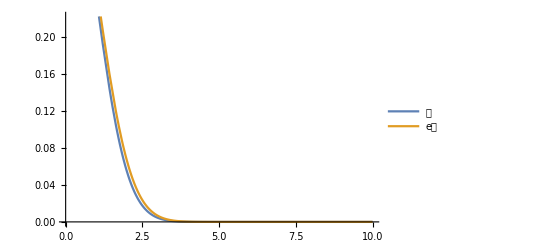

```mathematica
(* use Mathematica to estimate distribution parameters *)
Clear[data,x];
data=RandomVariate[𝒟=NormalDistribution[0,1],10^3];                           (* the more trials the more close to .. *)
e𝒟=EstimatedDistribution[data,NormalDistribution[μ,σ]]                        (* estimate distribution parameters μ,σ *)
Plot[{PDF[𝒟,x],PDF[e𝒟,x]},{x,0,10},PlotLegends->{"𝒟","e𝒟"}]        (* PDF plots should coincide *)
```

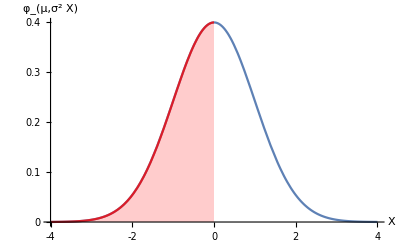

0.5

```mathematica
Clear[p1,p2];
p1=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-4,4},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,0.1,0.2,0.3,0.4,0.5}},AxesLabel->{X,Subscript[φ, μ,σ^2(X)]},AxesOrigin->{-4,0}];
p2=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-4,0},Filling->0,PlotStyle->{Red, Opacity[0.75]}];
Show[p1,p2]

(* What is the CDF at 0 ? .. half of the bell curve *)
CDF[NormalDistribution[0,1],0]//N
```

Every normal distribution is a version of the standard normal distribution whose domain has been stretched by a factor σ (the standard deviation) and then translated by μ (the mean value):

f(x|μ,σ^2) = 1/σ φ((x-μ)/σ)

The probability density must be scaled by 1/σ so that the integral is still 1.
If it is a standard normal deviate, the X=σZ+μ will have a normal distribution with expected value μ and standard deviation σ.
Conversely, if X is a normal deviate with parameters μ and σ^2, then Z=(X-μ) / σ will have a standard normal distribution. 
This variate is called the standardized form of X or Standard Score or also ‘z-score’.

z=(x-μ)/σ

Now above we saw what percentiles correspond to a certain standard deviation in a standard normal distribution.. and we came out with the standard rules of 68%, 95% and 99.7%. Let's say we wanna do the opposite.. see what Standard Score we get for a 50% area.. aka what standard deviation we have for outcomes that fall in the 50% of the distribution... we know that to cover 50% we need two halves of 25% each.. that's the percentile or quantile we need to associate a z-score (in a standard normal dist.. z=x=std) with. 

In Mathematica we have various ways to do that.. the most straightforward is the one that gets it from the inverse CDF. We already know that the CDF shows the probability a random variable X is found at a value equal to or less than a certain x.. i.e. it's how much area is under the curve at a certain point. Now given the area (here 50%) instead we wanna know what's the x that bound that area. The inverse of the CDF is called the percentage-point function and will give the outcome that is less than or equal to a single(point) probability.

Thus, if we write a CDF as :

F_X(x) = α = 1/2 erf[(-x+µ)/(√2 σ)], then we write its inverse as :

(F^-1)_X(α)=x, where α is our percent(ile)

```mathematica
InverseCDF[NormalDistribution[μ,σ],p]
InverseCDF[NormalDistribution[0,1],0.25]
```

ConditionalExpression[μ-√2 σ InverseErfc[2 p],0≤p≤1]

-0.67449

For a standard distribution, being μ=0 and σ=1 it all reduces to the inverse of the error function :

```mathematica
InverseErfc[2*0.25] √2
```

0.67449

We can try to use also Solve for x while using the direct CDF formula :

```mathematica
Quiet[Solve[1/2 Erf[(-x+µ)/(√2 σ)]==0.25,x]]
```

{{x→-0.67449 σ+1. µ}}

Other ways to calculate x from a percetile  :

```mathematica
(* this is actually the same as the above but with Mathematica symbolism *)
Quiet[Solve[CDF[NormalDistribution[0,1],x]==0.25,x]]
```

{{x→-0.67449}}

```mathematica
(* direct way *)
Quantile[NormalDistribution[0,1],{1/4,3/4}]//N
```

{-0.67449,0.67449}

BTW, what the outcome means ? 
That 50% of the values in a standard normal distribution are within -0.674 and (being a simmetrical distribution) +0.674 standard deviation.

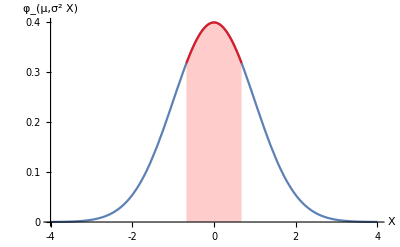

```mathematica
Clear[p1,p2];
p1=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-4,4},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,0.1,0.2,0.3,0.4,0.5}},AxesLabel->{X,Subscript[φ, μ,σ^2(X)]},AxesOrigin->{-4,0}];
p2=Plot[PDF[NormalDistribution[0,1],x]//Evaluate,{x,-0.67449,0.67449},Filling->0,PlotStyle->{Red, Opacity[0.75]}];
Show[p1,p2]
```

Examples

1) 90% of students at school are between 1.6m and 1.9m tall. 
Assuming the data is normally distributed, what is the mean and the standard deviation for this distribution ?

The mean is halfway between 1.6 and 1.9..

```mathematica
(1.6+1.9)/2
```

1.75

The mean is 1.75m
Now we know 95% is around 2 std. Let’s see what’s 90% ... 
(this would be done generally with z-score table)

```mathematica
Quiet[Solve[1/2 Erf[(-x+µ)/(√2 σ)]==0.45,x]]
```

{{x→-1.64485 σ+1. µ}}

With 90% we are around 1.65 std from the mean. So that’s 3.30 total standard deviations.
To calculate the standard deviation in meters we have just to calculate the range that corresponds to our 3.30 and divide it by that.

```mathematica
(1.9-1.6)/(1.65*2)
```

0.0909091

So our standard deviation is 9cm.

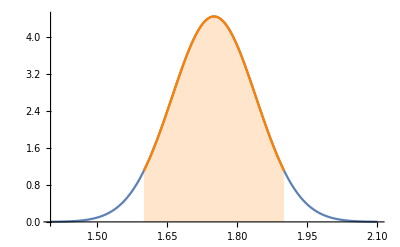

```mathematica
Clear[p1,p2];
p1=Plot[PDF[NormalDistribution[1.75,0.09],x]//Evaluate,{x,1.4,2.1},PlotRange->All];
p2=Plot[PDF[NormalDistribution[1.75,0.09],x]//Evaluate,{x,1.6,1.9},Filling->0,PlotRange->All,PlotStyle->{Orange}];
Show[p1,p2]
```

Now let’s check by integrating the PDF if our calculations were correct ... i.e. calculate the probability that a student is between 1.6 and 1.9 meter tall within the distribution with parameters we just calculated above.

```mathematica
Integrate[PDF[NormalDistribution[1.75,0.09],x],{x,1.6,1.9}]
Quantity[Round[%*100],"Percent"]//N
```

0.904419

90. %

2) In that same school one of our friends is 1.85 tall, how many standard deviations is he from the mean ?

For this we gonna use the z-score formula.

(x-μ)/σ

So we substract the mean from the student height and divide it by the standard deviation. This is called ‘standardization’.

```mathematica
(1.85-1.75)/0.09
```

1.11111

Our friend is just a tad more than 1 std from the mean. We can see it also intuitively as the std here is 0.09 (almost 10cm).. and the student is just 10cm from the mean.



3) Why standardize a normal distribution ? For example, let’s say a certain exam got the following results (out of 60 pts):

45, 33, 24, 42, 55, 58, 22, 18, 30, 48

The test must have been really hard, so the prof decides to standardize all the scores and only fail people 1 standard deviation below the mean. How many student will have to repeat the exam ?

```mathematica
Clear[scores]
scores = List[45,33,24,42,55,58,22,18,30,48];
Mean[scores]//N
```

37.5

So the mean is 37.5 pts. Now calculate the standard deviation for this normal distribution. We know that the variance of a distribution is the sum of the squared difference between the values and the mean divided by the number of values. Std is the square root of the variance.
However we can use Mathematica build-ins to calculate on-the-fly.

```mathematica
StandardDeviation[scores]//N
```

14.1126

We have a std of 14 pts.

Now we know from the above formula how to standardize a distribution.. substract from each value the mean and eventually divide by the std, the result will be a standard normal dist where each value is actually the standard deviation of the value in the original list.
However we can use Mathematica just for that :)

```mathematica
stdScores=Standardize[scores]//N
{Mean[stdScores],Variance[stdScores]}; (*check back to see if we have μ=0, σ=1*)
Select[stdScores,#<-1&](*select those values less than -1 std*)
```

{0.531438,-0.318863,-0.956589,0.318863,1.24002,1.4526,-1.09831,-1.38174,-0.531438,0.744014}

{-1.09831,-1.38174}

We see that only 2 students will have to repeat the exam (the ones lower than -1 standard deviation). Of course they corresponds to the lowest exam scores.. 22(-1.098) and 18(-1.38). Go back studying you donkeys ! ;)

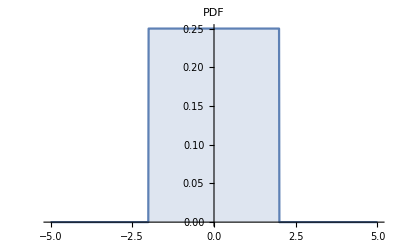
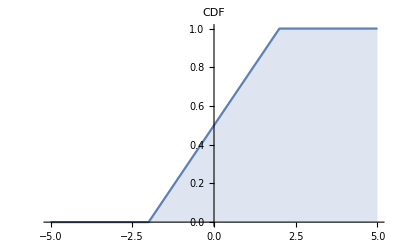

```mathematica
Clear[x];
𝒟=HistogramDistribution[stdScores];
DiscretePlot[#[𝒟,x],{x,-5,5,.01},PlotLabel->#]&/@{PDF,CDF}
```

4) A company manufactures nails with length normally distributed, mean 0.497 inches, and standard deviation 0.002 inches. 
Find the fraction that satisfies the specification of length equal to 0.5 inches plus/minus 0.004 inches:

```mathematica
Clear[𝒟];
𝒟=NormalDistribution[Quantity[.497,"Inches"],Quantity[.002,"Inches"]]
Probability[Quantity[ .5-.004,"in"]<x<Quantity[.5+.004,"in"],x\[Distributed] 𝒟]

(*Direct computation with the CDF*)
CDF[ 𝒟,Quantity[.5+.004,"in"]]-CDF[ 𝒟,Quantity[.5-.004,"in"]]
```

QuantityDistribution[NormalDistribution[0.497,0.002], in]

0.69123

0.69123

5) Compute and illustrate the continuous probability P(1/2<x⩽1) for a standard normal distribution.

{1/2 (-Erf[1/(2 √2)]+Erf[1/(√2)]),0.149882}

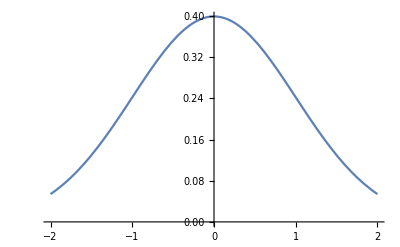
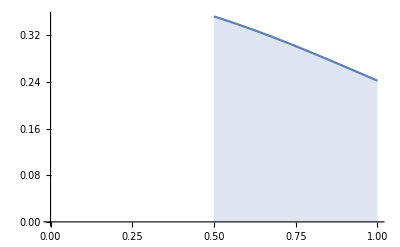

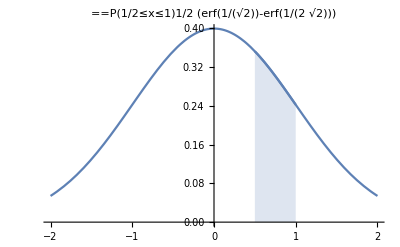

```mathematica
Clear[p,p1,p2];
p=Probability[1/2<x≤1,x\[Distributed]NormalDistribution[0,1]];
{p,p//N}

{p1,p2}={Plot[PDF[NormalDistribution[0,1],x],{x,-2,2}],Plot[PDF[NormalDistribution[0,1],x],{x,1/2,1},AxesOrigin->{0,0},Filling->Axis]}

Show[p1,p2,PlotLabel->Style[Row[{P[1/2≤x≤1],p},"="],Small]]
```

```mathematica
(*of course we can also manually integrate the PDF for the above P*)
Integrate[PDF[NormalDistribution[0,1],x],{x,1/2,1}]//N
```

0.149882

6) An average light bulb manufactured lasts 300 days with a standard deviation of 50 days. Assuming that bulb life is normally distributed, what is the probability that a light bulb will last at most 365 days ?

Now, x is 365; the mean is 300 and the std is 50 days.

```mathematica
CDF[NormalDistribution[300,50],365]//N
```

0.9032

7) Suppose scores of an IQ test are normally distributed. If the test has a mean of 100 and a standard deviation of 10, what is the probability that a person who takes the test will score between 90 and 110?

Basically we need to compute the probability at each score and substract them to get the probability in between those twos.

```mathematica
(CDF[NormalDistribution[100,10],110]-CDF[NormalDistribution[100,10],90])//N
```

0.682689

8) Ninety-five percent of all cultivated strawberry plants grow to a mean height of 11.4 cm with a standard deviation of 0.25 cm.
If 225 plants in the greenhouse have a height between 11.15 cm and 11.65 cm, how many plants were in the greenhouse ?
And how many plants in the greenhouse would we expect to be shorter than 10.9 cm ?

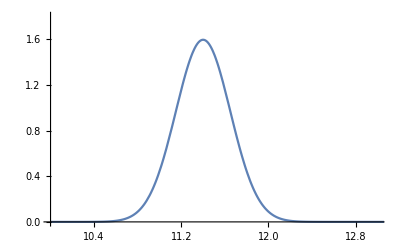

0.682689

331

0.0227501

7.53029

```mathematica
Clear[𝒟,p1,p2];
𝒟=NormalDistribution[11.4,.25];
Plot[PDF[𝒟,x],{x,10,20},PlotRange->{{10,13},{0,1.8}}]

p1=CDF[𝒟,11.65]-CDF[𝒟,11.15]//N (*calculate probability for these heights*)
totNPlants=Round[225/0.68](*total number of plants*)

p2=CDF[𝒟,10.9](*probability of being shorter than 10.9cm*)
totNPlants*p2(*number of plants that short*)
```

9) The average life expectancy for a dog is 10 years 2 months with a standard deviation of 9 months.
What would be the lifespan of almost all dogs (99.7%) ?
In a sample of 825 dogs, how many dogs would have life expectancy between 9 years 5 months and 10 years 11 months ?
How many dogs, from the sample, would we expect to live beyond 10 years 11 months?

122

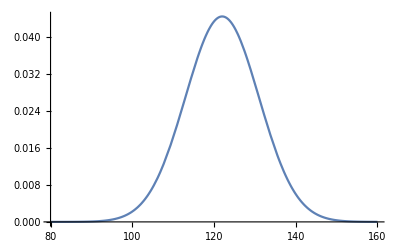

{{x→-26.7096+1. µ}}

7.94167

12.3917

{0.158655,0.841345}

0.682689

563.219

693.

132.

```mathematica
Clear[μ,σ,prob,mu,sigma];
(*convert years to months*)
μ=(10*12)+2
σ=9;

(*rig the distribution*)
𝒟=NormalDistribution[μ,σ];

(*plot ta shit*)
Plot[PDF[𝒟,x],{x,80,160},PlotRange->Full]

Quiet[Solve[1/2 Erf[(-x+µ)/(√2 σ)]==0.997/2,x]](*result is in months for standard normal dist.. close to 3std.. 9*3=27*)

(122-26.7)/12//N (*min years of expected life*)
(122+26.7)/12//N (*max years of expected life*)

prob=CDF[𝒟,{(9*12)+5,(10*12)+11}]//N
%[[2]]-%[[1]]
825*% (*dogs to live between the time range*)

825*0.84(*0.84 is p[[2]]*)
825-%(*how many dogs expected to live more than*)
```

Probability properties

0

1

1/2

True

True

True

(√2)/(π (1+x^4))

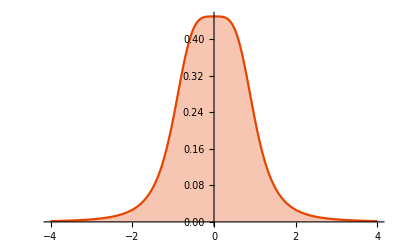

(x≈ProbabilityDistribution[(√2)/((1+x^4) π),{x,-∞,∞}])==(x\[Distributed]ProbabilityDistribution[(√2)/((1+x^4) π),{x,-∞,∞}])

NormalDistribution[244+b,18]

```mathematica
Clear[𝒟,a,b,x,y];

(*The probability of an impossible event is 0:*)
Probability[x<3,x\[Distributed]UniformDistribution[{3,5}]]

(*The probability of a certain event is 1:*)
Probability[3<x<5,x\[Distributed]UniformDistribution[{3,5}]]

(*The probability of an arbitrary event must lie between 0 and 1:*)
Probability[1<x<4,x\[Distributed]UniformDistribution[{3,5}]]

(*The probability of an event in a continuous distribution is defined by an integral:*)
𝒟=NormalDistribution[];
Probability[E^x < 3, x \[Distributed] 𝒟] == ∫_(-∞)^∞ Boole[E^x<3]PDF[𝒟,x]ⅆx

(*The probability of an event in a discrete distribution is defined by a sum:*)
𝒟=PoissonDistribution[1];
Probability[E^x < 3, x \[Distributed] 𝒟] == ∑_(x=-∞)^∞ Boole[E^x<3]PDF[𝒟,x]

(*The probability of an event is equivalent to the Expectation of the Boole of the event:*)
𝒟=ExponentialDistribution[2];
Probability[1<x<3,x\[Distributed]𝒟]==Expectation[Boole[1<x<3],x\[Distributed]𝒟]

(*Define a continuous probability distribution:*)
𝒟=ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-Infinity,Infinity}];
PDF[𝒟,x]
Plot[%,{x,-4,4},Filling->Axis,PlotTheme->"WarmColor"]

(*Both are equivalent ways to assert that x is distributed according to the probability distribution*)
x≈𝒟==Distributed[x,𝒟]

(*Simple transformations of random variables:*)
TransformedDistribution[2 u+b,u\[Distributed]NormalDistribution[μ,σ]]
```

The Central Limit Theorem

The central limits theorem states that the sum of a sufficiently larger number of i.i.d.(indipendent and identically distributed) random variables tends to a normal distribution. In other words, if an experiment is repeated a large number of times, the outcome on average approaches a normal distribution. Specifically, given i.i.d. random variables X_i, i=1,...N, each with the mean E[X_i]=μ and variance Var[X_i]=σ^2, their sum converges to :

∑_(i=1)^N X_i -> 𝒩(μN,σ^2 N), as N→∞

To illustrate the theorem, let us consider the sum of uniform random variables X_i~𝒰(-1, 1). The mean and variance of the random variable are E[X_i]=0 and Var[X_i]=1/3, respectively. By the central limit theorem, we expect their sum, Z_N, to approach

Z_N=(1/(√N)∑)_(i=1)^N X_i -> 𝒩(μN,σ^2 N) = 𝒩(0,N/3) as N->∞

That means here we’re not interested in averaging the random variates x_j but in averaging the random variables X_N (i.e. X^- , aka Xbar).

{0,1/3,1/(√3)}

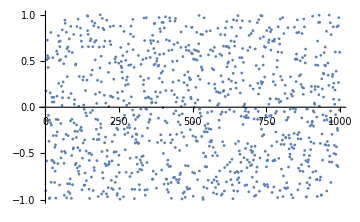
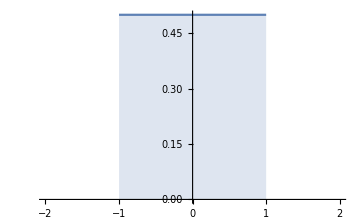

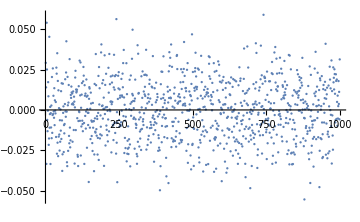
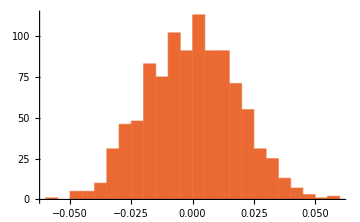

```mathematica
Clear[𝒟,data];

𝒟=UniformDistribution[{-1,1}];(*any distribution could be here.. even a discrete one*)
{Mean[𝒟],Variance[𝒟],StandardDeviation[𝒟]}

data:=RandomVariate[𝒟,1000]; (*be aware of the SetDelayed.. to get different numbers each time we call data*)
{ListPlot[data,ImageSize->Medium],Plot[PDF[𝒟,x]//Evaluate,{x,-1,1},PlotRange->{{-2,2},{0,0.5}},Filling->Axis,ImageSize->Medium]}

ndata=Table[Mean[data], 1000];
{ListPlot[ndata,ImageSize->Medium],Histogram[ndata,PlotTheme->"WarmColor",ImageSize->Medium]}
```

Use histograms when you have continuous measurements and want to understand the distribution of values and look for outliers for example. These graphs take your continuous measurements and place them into ranges of values known as bins. Each bin has a bar that represents the count or percentage of observations that fall within that bin, you can move the mouse cursor over the bins to get that in a ‘baloon’.

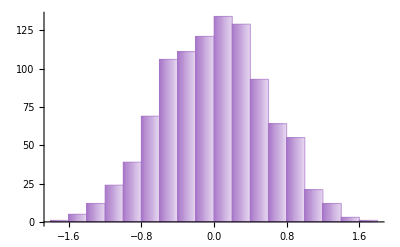

```mathematica
(*using the same data above, directly using the CLT equation*)
n=5000;
Subscript[Z, n]=1/(√n)∑_(i=1)^n data;
Histogram[Subscript[Z, n],PlotTheme->"RoyalColor",ChartElementFunction->"FadingRectangle"]
```

What we see here is that for large enough n, the distribution of X̄ is close to the normal distribution with mean μ and variance σ^2/n. The usefulness of the theorem is that the distribution of √n((X̄)_n-μ) approaches normality regardless of the shape of the distribution of the individual X_i. Formally it states that, as 𝓃 approaches ∞ , the random variables √n((X̄)_n-μ) converge in distribution to a normal 𝒩(0,σ^2).


Now, let’s see another case where using the CLT can be meaningful (ie. Re-sampling).
For the above case, the meaningfulness of the CLT is that by approaching the same experiment N times we can get a normal average of the single outcome that better represent the expected outcome as we are approaching it with random numbers that will give every time a slighty different result.

For example let’s say we wanna estimate the statistics for a certain population .. 
like a bunch of students in a lab, like how many times they pick up their phone during the lesson. 
Let’s first model this :

```mathematica
Clear[data,Ntot];
SeedRandom[12345];
Ntot=100;
data = RandomInteger[{0,500},Ntot];(* 100 students can variably pick-up the phone up to 500 times a day *)

{Mean[data]//N,"→ mean"}
{StandardDeviation[data]//N,"→ std"}
{standardError = %/√Ntot,"→ standard error"}
```

{252.55,→ mean}

{142.569,→ std}

{{14.2569,(→ std)/10},→ standard error}

So we see that from the whole population we can get our statistics well defined.
The average number of times a student pick up his phone is ≃255.
The standard deviation is ≃142.

Now, let’s say that we don’t have access to the whole population but at time to only a subset of that. Let’s say 30 students each time.
We still wanna know the statistics for the _whole_ population from that.

```mathematica
Clear[tData,Npar];
SeedRandom[123456];
Npar=30;
tData = RandomChoice[data,Npar]; (* choose randomly 30 students from the whole population *)
{Mean[tData]//N,"→ mean"}
{StandardDeviation[tData]//N,"→ std"}
```

{274.067,→ mean}

{130.093,→ std}

(Btw, the above is called: a point estimate).
But we see that comparing the mean of the whole population to the partial mean we have a big discrepancy. Same for σ.
How much is this discrepancy ? The standard error of the sample mean .. ie. σ/√N(we’ll see this better in part2).

```mathematica
Clear[σ];
σ=StandardDeviation[tData]//N;
{Subscript[σ, eer]=σ/√Npar, "→ estimated std error"}
{Subscript[σ, ter]=StandardDeviation[data]/√Npar//N, "→ theoretical std error"}
```

{23.7516,→ estimated std error}

{26.0293,→ theoretical std error}

So we see that each time we sample just 30 students, we ain’t gonna estimate the real statistics for the entire population.
What we gonna do then ? :) Let’s use the CLT !

{252.643,→ estimated mean}

{252.55,→ theoretical mean}

{25.8815,→ estimated std error}

{26.0293,→ theoretical std error}

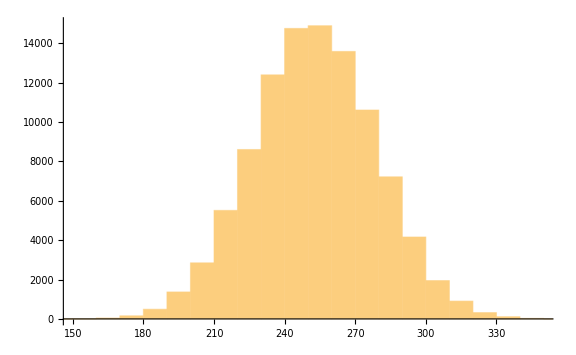

```mathematica
(* choose 100000 times different bunches of 30 students, aka re-sampling *)
simData = Table[Mean[RandomChoice[data,Npar]],10^5]; 

{Mean[simData]//N,"→ estimated mean"}
{Mean[data]//N,"→ theoretical mean"}

{StandardDeviation[simData]//N,"→ estimated std error"}
{Subscript[σ, ter]=StandardDeviation[data]/√Npar//N, "→ theoretical std error"}

Histogram[simData,ImageSize->Large,PlotRange->{{150,350},{0,15000}}]
```

Now, let’s try the same resampling but with a sample size of 300 (was 30 prev).

270

{252.59,→ estimated mean}

{252.55,→ theoretical mean}

{8.65795,→ estimated std error}

{8.67644,→ theoretical std error}

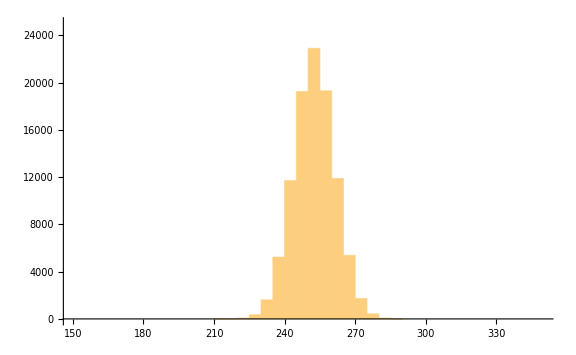

```mathematica
(* choose 100000 times different bunches of 270 students, aka re-sampling *)
Npar=270
simData = Table[Mean[RandomChoice[data,Npar]],10^5]; 

{Mean[simData]//N,"→ estimated mean"}
{Mean[data]//N,"→ theoretical mean"}

{StandardDeviation[simData]//N,"→ estimated std error"}
{Subscript[σ, ter]=StandardDeviation[data]/√Npar//N, "→ theoretical std error"}

Histogram[simData, ImageSize->Large,PlotRange->{{150,350},{0,25000}}]
```

First thing to notice is that our std error has been drastically reduced. By how much ? 1/3 and why is it like that ? ;)

```mathematica
√10//N
```

3.16228

Because the convergence rate in MC is √n. 
So let’s see it the other way around. How much we need to increase our sample size to get a 3x less error ? 3^2 .. 30*9=270. 

Another cool thing to notice above is about the narrower shape of our normal distribution. Why is it getting narrower ?
Because using more samples allow us to have more estimates around the true outcome .. which is ~250 (just look at the graph). 
Also the narrower the higher the PDF (around graph y-axis point), that means we have more probability to get those outcomes.

We can also use this to visually understand what convergence means here. Getting closer and closer in distribution to the true value.

Because the standarddeviation for a distribution can also be seen as a shape shrinking factor, we expect to have bigger std for dist with longer tail.

```mathematica
Npar=30;
simData = Table[Mean[RandomChoice[data,Npar]],10^5]//N;
e𝒟=EstimatedDistribution[simData,NormalDistribution[μ,σ]]

Npar=270;
simData = Table[Mean[RandomChoice[data,Npar]],10^5]//N; 
e𝒟=EstimatedDistribution[simData,NormalDistribution[μ,σ]]

FindDistributionParameters[simData,NormalDistribution[μ,σ]] (* same as above *)

FindDistribution[simData] (*let's say we don't even know what distribution underline the data we have *)
(* depending on the random data it may sometimes output a mixturedistribution.. *)
```

NormalDistribution[252.69,25.8865]

NormalDistribution[252.565,8.60746]

{μ→252.565,σ→8.60746}

NormalDistribution[252.761,8.48183]

Transformations of Continuous Random Variables

The transformation of a random variable X by a function ℊ produces another random variable, Y,and we denote this by

Y=g(X)

We described the random variable X by distribution

P(x≤X≤x+dx)=f_X(x)dx

and the transformed variable by 

P(y≤Y≤y+dy)=f_Y(y)dy

Substitution of y=g(x) and dy=g'(x)dx and noting g(x)+g'(x)dx=g(x+dx) results in 

f_Y (y) dy = P (g (x) <= g(X) <= g(x) +g'(x) dx = P(g(x)<=g(X)<=g(x+dx))=P(x<=X<=x+dx)=f_X(x)dx

aka, f_Y(y)dy=f_X(x)dx

We can manipulate the expression to obtain an explict expression for f_Y in terms of f_X and ℊ
First we note (from monotonicity) that 

y=g(x) ⇒ x=g^-1(y) and dx=dg^-1/dydy

substituting in the above yields

f_Y(y)dy = f_X(x)dx = f_X(g^-1(y))dg^-1/dydy
f_Y(y) = f_X(g^-1(y))dg^-1/dy

Conversely, we can obtain an explicit expression for f_X in terms of f_Y and g. From y=g(x) and dy=g'(x)dx, we obtain

f_X(x)dx=f_Y(y)dy=f_Y(g(x))g'(x)dx ⇒ f_X(x)=f_Y(g(x))g'(x)

Eventually, assuming X takes on a value between a and b, and Y takes on a value between c and d, the mean of Y is

E[Y] = ∫_c^d yf_Y(y)ⅆy = ∫_a^b g(x)f_X(x)ⅆx

where the second equality follows from f_Y(y)dy = f_X(x)dx and y=g(x)


Examples

1) Standard uniform distribution to a general uniform distribution

From a standard U∼𝒰(0,1) we wanna generate a general uniform distribution X~𝒰(a,b) defined  on the interval [a,b].
Because a uniform distribution is uniquely determined by the two end points, we simply need to map the end point 0 to a and the point 1 to b. This is accomplished by the transformation : 

g(u) = a+(b-a)u

Thus, 𝒳~𝒰(a,b) is obtained by mapping U~𝒰(0,1) as 

X = a+(b-a)U

{0.824615,0.769555,0.721831,0.960099,0.409459,0.0709144,0.745245,0.301749,0.9741,0.0923722}

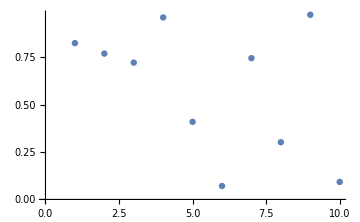

{4.82461,4.76955,4.72183,4.9601,4.40946,4.07091,4.74525,4.30175,4.9741,4.09237}

{4.82461,4.76955,4.72183,4.9601,4.40946,4.07091,4.74525,4.30175,4.9741,4.09237}

{4.82461,4.76955,4.72183,4.9601,4.40946,4.07091,4.74525,4.30175,4.9741,4.09237}

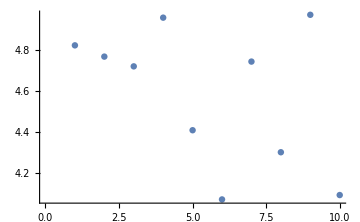

```mathematica
Clear[𝒟,a,b];

𝒟=UniformDistribution[{0,1}];
stdUData=RandomVariate[𝒟,10]
ListPlot[stdUData,ImageSize->Medium]

fromStdToGen[a_Real, b_Real,k_Real]:=a+(b-a)*k;
{a=4,b=5};

(*various ways to 'map' a fnc with multiple args *)
genUData=Map[fromStdToGen[a,b,#]&,stdUData]//N   (*use # to specify what fnc arg to map*)
genUData=fromStdToGen[a,b,#]&/@stdUData//N            (*same as above using /@ instead of Map*)
genUData=Thread[fromStdToGen[a,b,stdUData]]//N

ListPlot[genUData,ImageSize->Medium]
```

2) Standard normal distribution to a general normal distribution

We have a standard normal distribution Z~𝒩(0,1) and wanna map it to a general normal distribution X~𝒩(μ,σ^2). 
The transformation is given by:

X = μ+σZ

X will have a normal distribution with expected value μ and standard deviation σ. We already saw the opposite transformation when dealing with z-score (aka. standardization).

Algebra of Random Variables

In principle, the elementary algebra of random variables is equivalent to that of conventional non-random (or deterministic) variables. However, the changes occurring on the probability distribution of a random variable obtained after performing algebraic operations are not straightfoward. Therefore, the behavior of the different operators of the probability distribution, such as expected values, variances, covariances, and moments, may be different from that observed for the random variable using symbolic algebra.


Elementary symbolic algebra of random variables

Z = X+Y = Y+X
Z = X-Y = -Y+X
Z = X*Y = Y*X
Z = X/Y = (1/Y)*X
Z = X^Y = e^(Yln(x))

In all cases, the variable Z resulting from each operation is also a random variable. All commutative and associative properties of conventional algebraic operations are also valid for random variables. If any of the random variables is replaced by a deterministic variable or by a constant value, all the previous properties remain valid.


Expectation algebra

The expected value E of the random variable Z resulting from an algebraic operation between two random variables can be calculated with:

E[Z] = E[X+Y] = E[X]+E[Y] = E[Y]+E[X]
E[Z] = E[X-Y] = E[X]-E[Y]
E[Z] = E[XY] = E[YX] If independent, then: E[XY] = E[X]E[Y] = E[Y]E[X]
E[Z] = E[X/Y] = E[(1/Y)X] If independent, then: E[X/Y] = E[X]E[1/Y] = E[1/Y]E[X]
E[Z] = E[X^Y] = E[ℯ^(Yln(X))]

If any of the random variables is replaced by a deterministic variable or by a constant value, the previous properties remain valid considering that P[X=k]=1 ⇒ E[X]=k


Variance algebra

Var[Z] = Var[X+Y] = Var[X] + 2Cov[X,Y] + Var[Y] If independent Var[X+Y] = Var[X]+Var[Y]
Var[Z] = Var[X-Y] = Var[X] - 2Cov[X,Y] + Var[Y] If independent Var[X+Y] = Var[X]+Var[Y] (same as for addition)
Var[Z] = Var[XY] = Var[YX] If independent  Var[XY] = E[X^2]E[Y^2]-(E[X]E[Y])^2 = Var[X]Var[Y]+Var[X](E[Y])^2+Var[Y](E[X])^2
Var[Z] = Var[X/Y] = Var[X(1/Y) If independent  Var[X/Y] = E[X^2]E[1/Y^2]-(E[X]E[1/Y])^2 = Var[X]Var[1/Y]+Var[X](E[1/Y])^2+Var[1/Y](E[X])^2
Var[Z] = Var[X^Y] = Var[e^(Yln(X))]
where Cov[X,Y]=Cov[Y,X]

The variance of a random variable can also be expressed directly in terms of the covariance or in terms of the expected value:

Var[X] = Cov(X,X) = E[X^2]-E[X]^2

If any of the random variables is replaced by a deterministic variable or by a constant value the previous properties remain valid considering that P[X=k]=1 and E[X]=k, Var[X]=0 and Cov[Y,k]=0
Special cases are the addition and multiplication of a random variable with a deterministic variable or a constant, where:

Var[X+Y] = Var[Y]
Var[kY] = k^2 Var[Y]


Covariance algebra

Cov[Z,X] = Cov[X+Y,X] = Var[X]+Cov[X,Y] where if independent Cov[X+Y,X] = Var[X]
Cov[Z,X] = Cov[X-Y,X] = Var[X]-Cov[X,Y] where if independent Cov[X-Y,X] = Var[X]
Cov[Z,X] = Cov[XY,X] = E[X^2 Y]-E[XY]E[X] and if independent Cov[XY,X] = Var[X]E[Y]
Cov[Z,X] = Cov[X/Y,X] = E[X^2/Y]-E[X/Y]E[X] if independent Cov[X/Y,X] = Var[X]E[1/Y]  (div, covariance with respect to the numerator)
Cov[Z,X] = Cov[Y/X,X] = E[Y]-E[Y/X]E[X] and if independet Cov[Y/X,X] = E[Y](1-E[X]E[1/X]) (div, covariance with respect to the denominator)
Cov[Z,X] = Cov[X^Y,X] = E[X^(Y+1)]-E[X^Y]E[X] (exp, covariance with respect to the base)
Cov[Z,X] = Cov[Y^X,X]=E[XY^X]-E[XY^X]-E[Y^X]E[X] (exp, covariance with respect to the power)

The covariance of a random variable can also be expressed directly in terms of the expected value:

Cov(X,Y) = E[XY]-E[X]E[Y]

If any of the random variables is replaced by a deterministic variable or by a constant value the previous properties remain valid considering that: E[k]=k, Var[k]=0 and Cov[X,k]=0

# Probability Theorems

Slutsky’s Theorem

https://bookdown.org/ts_robinson1994/10_fundamental_theorems_for_econometrics/slutsky.html

Continuous mapping theorem

https://en.wikipedia.org/wiki/Continuous_mapping_theorem

# Probability Theory with Mathematica build-ins

We now re-cap Mathematica simbolism to approach probability theory

```mathematica
Clear[𝒟];
```

Get PDF and CDF for known distributions :

```mathematica
𝒟=NormalDistribution[μ,σ];
PDF[𝒟]
CDF[𝒟]
```

Exp[-1/2 ((#1-μ)/σ)^2]/(σ √(2 π))&

1/2 Erfc[(μ-#1)/(√2 σ)]&

The CDF F(x) is the integral of the PDF f(x) for continuous distributions; F(x)==∫_(-∞)^x f(ξ)ⅆξ :

```mathematica
Clear[x];
Integrate[PDF[ExponentialDistribution[λ],ξ],{ξ,-∞,x},Assumptions->x∈Reals&&λ>0]
CDF[ExponentialDistribution[λ],x]
FullSimplify[%%-%,λ>0]
```

Piecewise[{{ⅇ^(-x λ) (-1+ⅇ^(x λ)), x>0}, {0, True}}]

Piecewise[{{1-ⅇ^(-x λ), x≥0}, {0, True}}]

0

Mean, variance and covariance :

```mathematica
Mean[𝒟]
Variance[𝒟]
Covariance[UniformDistribution[{{a,b},{c,d}}]]//MatrixForm
```

μ

σ^2

(1/12 (-a+b)^2 | 0
0 | 1/12 (-c+d)^2)

Calculate probability that x falls within a range :

```mathematica
Clear[x];
p=Probability[1/5<x≤1,x\[Distributed]𝒟]
p=NProbability[1/5<x≤1,x\[Distributed]𝒟]
p=Probability[x==1,x\[Distributed]𝒟](* prob x will be exactly 1 ;) *)
```

1/2 (Erfc[(-1+μ)/(√2 σ)]-Erfc[(-1/5+μ)/(√2 σ)])

NProbability[1/5<x≤1,x\[Distributed]NormalDistribution[μ,σ]]

0

Calculate expectation of f of x with respect to the distribution :

```mathematica
𝒟=PoissonDistribution[1];
ExpectedValue[x^4,𝒟,x]
```

15

Assert x is uniformly distributed :

```mathematica
Distributed[x, UniformDistribution]
```

x\[Distributed]UniformDistribution

Generate 10 random variates distributed accordling to the distribution :
(aka, draw 10 random numbers from the distribution .. )

```mathematica
𝒟= UniformDistribution[];
RandomVariate[𝒟,10]
```

{0.128696,0.795484,0.595903,0.866634,0.118013,0.734915,0.460884,0.684511,0.355839,0.618871}

Get the characteristic function for the distribution as a function of t : 1.0 / (4.0 * M_PI)

```mathematica
CharacteristicFunction[𝒟,t]
```

-(ⅈ (-1+ⅇ^(ⅈ t)))/t

Define a custom probability distribution by its PDF:

(√2 (1+x^4))/π

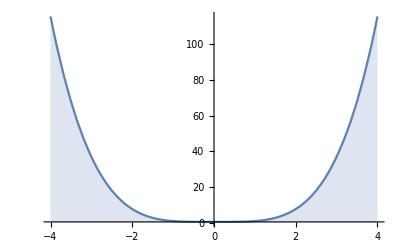

(√2 (5 x+x^5))/(5 π)

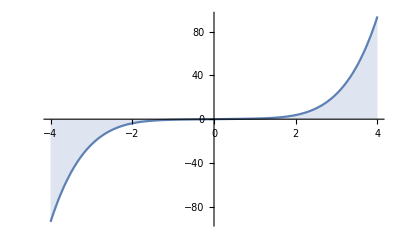

```mathematica
Clear[x];
𝒟=ProbabilityDistribution[ Sqrt[2]/Pi*(1+x^4),{x,-Infinity,Infinity}];
PDF[𝒟,x]
Plot[%, {x,-4,4},Filling->Axis,PlotRange->Full]
CDF[𝒟,x]
Plot[%, {x,-4,4},Filling->Axis,PlotRange->Full]
```

Define a custom probability distribution by a given piecewise PDF :

Piecewise[{{0, x≤0}, {k (x^2/2+x^3/3), 0<x≤1}, {(5 k)/6, True}}]

Piecewise[{{6/5 (x+x^2), 0≤x≤1}, {0, True}}]

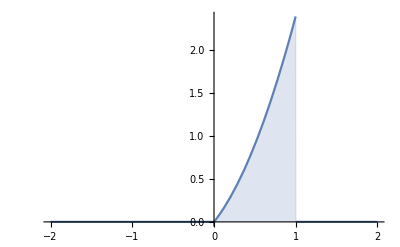

Piecewise[{{1, x>1}, {1/5 (3 x^2+2 x^3), 0<x≤1}, {0, True}}]

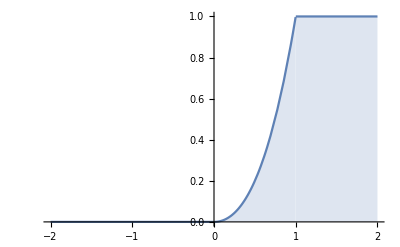

```mathematica
Clear[x];
pdf=Piecewise[{{k(x^2+x),0≤x≤1}}];                (* need to get k in a way that the piecewise integrates to 1 first*)
                                                                                                      (* see part3 Normalizing Constant *)
Integrate[pdf,x]                                                                (* here we see that for 1 it is 5k/6 so k for the pdf is 6/5 *)
pdf=Piecewise[{{6/5(x^2+x),0≤x≤1}}];           (* now we can use it as a pdf coz it's actually a pdf ;) *)
𝒟=ProbabilityDistribution[ pdf,{x,-Infinity,Infinity}];

PDF[𝒟,x]
Plot[%, {x,-2,2},Filling->Axis,PlotRange->Full]
CDF[𝒟,x]
Plot[%, {x,-2,2},Filling->Axis,PlotRange->Full]
```